```mathematica
createImage[noise_] :=ImageEffect[ Image@ConstantArray[0.5, {500,500}], {"GaussianNoise", noise}];
```

```mathematica
Image@ConstantArray[0.5, {500,500}]
```

-Graphics-

```mathematica
createImage[0.1]
```

-Graphics-

```mathematica
images = Table[createImage[0.03], 500];
calibration = Image@ConstantArray[0.5, {500,500}];
```

```mathematica
VideoGet[range_]:=images[[range]];

BackgroundFnMean[range_?VectorQ]:=Image@Mean[ImageData/@(VideoGet@range)];

BackgroundFnMedian[range_?VectorQ]:=Image@Median[ImageData/@(VideoGet@range)];

BackgroundFnSmartMean[range_?VectorQ]:=Module[{RunBGAnalysis},RunBGAnalysis[sum0_,n0_,attemptsLeft_]:=Module[{frames,sum,n,ComputeN,ns},frames=RandomSample[VideoGet@RandomSample[range,Min[200,Length@range]]];
FindStationaryPoints[i_]:=Module[{d1,d2,filterAt},filterAt=0.025;(*set where to binirize imges*)d1=ImageDifference[frames[[i-1]],frames[[i]]]//Binarize[#,filterAt]&//ColorNegate;
d2=ImageDifference[frames[[i]],frames[[i+1]]]//Binarize[#,filterAt]&//ColorNegate;
ImageMultiply[d1,d2]];
ns=FindStationaryPoints/@Range[2,Length@frames-1];
n=n0+Total[ImageData/@ns];
sum=sum0+Total[ImageData/@Thread[ImageMultiply[frames[[#]],ns[[#-1]]]&/@Range[2,Length@frames-1]]];
(*return result*)If[(MemberQ[n,0.0,2]||MemberQ[n,1.0,2])&&attemptsLeft>0,RunBGAnalysis[sum,n,attemptsLeft-1],Image@(sum/n)]];
RunBGAnalysis[0,0,4]];
```

#### Testing

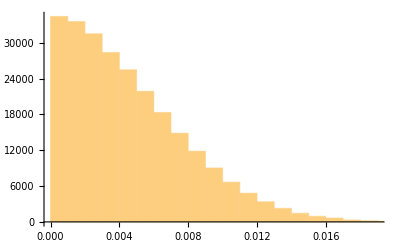

```mathematica
BackgroundFnMean[Range[100]]~ImageDifference ~ calibration //ImageData // Flatten // Histogram
```

```mathematica
BackgroundFnMean[Range[100]]~ImageDifference ~ calibration //ImageData // Flatten // Mean
```

0.0046071

```mathematica
testAlgorithm[ image_, calibration_]:= StandardDeviation@Flatten@ImageData@ ImageDifference[ image, calibration];
testAlgorithmHistogram[ image_, calibration_]:= Histogram@Flatten@ImageData@ ImageDifference[ image, calibration];
```

0.00080803

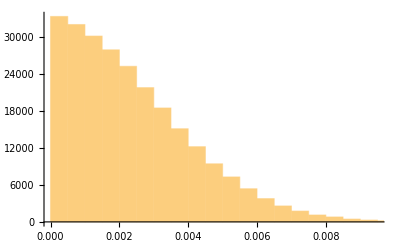

```mathematica
testAlgorithm[ BackgroundFnMean[Range[500]], calibration]
testAlgorithmHistogram[ BackgroundFnMean[Range[100]], calibration]
```

0.00130368

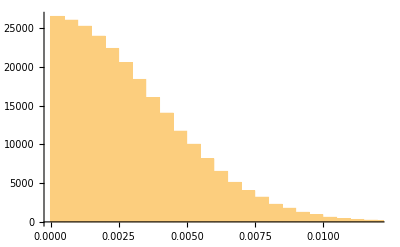

7.29789

```mathematica
testAlgorithm[ BackgroundFnMedian[Range[300]], calibration]
testAlgorithmHistogram[ BackgroundFnMedian[Range[100]], calibration]
AbsoluteTiming[BackgroundFnMedian[Range[300]]][[1]]
```

0.0023019

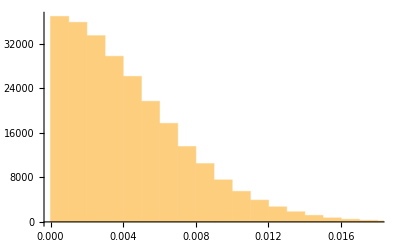

6.50574

```mathematica
testAlgorithm[ BackgroundFnSmartMean[Range[500]], calibration]
testAlgorithmHistogram[ BackgroundFnSmartMean[Range[100]], calibration]
AbsoluteTiming[BackgroundFnSmartMean[Range[500]]][[1]]
```

#### => Median algorithm has better noise characterestics than the Smart algoithm